```mathematica
Clear[f,w,t,a,b];
w[b_,a_]:=a I+b;
f[z_,a_,b_,al_]:=(1+al w[a,b]/2) z^2-(al-(3 al+4) w[a,b]/2) z-(1+al);
t[a_,b_,al_]:=NSolve[f[z,a,b,al]==0,z];
RegionPlot3D[Norm[t[a,b,al][[1,1,2]]]≤1&&Norm[t[a,b,al][[2,1,2]]]≤1,{a,-5,5},{b,-5,5},{al,-2,0}]
```

-Graphics3D-

```mathematica
(*五阶Adams-Bashforth*)
```

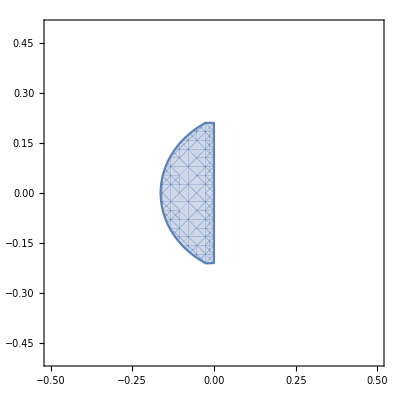

```mathematica
Clear[f,w,t,a,b];
w[b_,a_]:=a I+b;
f[z_,a_,b_]:=z^5-z^4-w[a,b]/720 (1901 z^4-2774 z^3+2616 z^2-1274 z+251);
t[a_,b_]:=NSolve[f[z,a,b]==0,z];
RegionPlot[Norm[t[a,b][[1,1,2]]]≤1&&Norm[t[a,b][[2,1,2]]]≤1&&Norm[t[a,b][[3,1,2]]]≤1&&Norm[t[a,b][[4,1,2]]]≤1&&Norm[t[a,b][[5,1,2]]]≤1,{a,-0.5,0.5},{b,-0.5,0.5}]
```

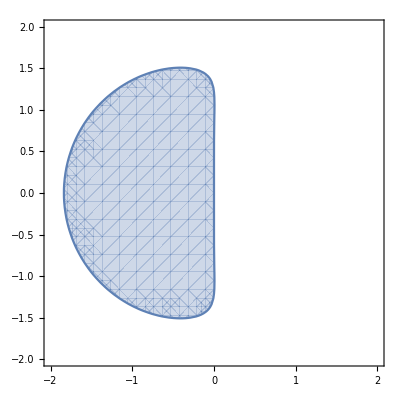

```mathematica
Clear[f,w,t,a,b];
w[b_,a_]:=a*I+b;
f[z_,a_,b_]:=(1-251*w[a,b]/720)*z^4+(-1-646*w[a,b]/720)*z^3+(264*w[a,b]/720)*z^2+(-106*w[a,b]/720)*z+(19*w[a,b]/720);
t[a_,b_]:=Solve[f[z,a,b]==0,z];
RegionPlot[Norm[t[a,b][[1,1,2]]]≤1&&Norm[t[a,b][[2,1,2]]]≤1&&Norm[t[a,b][[3,1,2]]]≤1&&Norm[t[a,b][[4,1,2]]]≤1,{a,-2,2},{b,-2,2}]
```